```mathematica
n=17;
itmax=17000;
e=ConstantArray[1,n];
trial=ConstantArray[0,itmax];
```

```mathematica
dom=ConstantArray[1,{n,n}];
For[i=1,i≤n,i++,
For[j=1,j≤i,j++,
dom[[i,j]]=0;
]
];
mu=dom.e/n;
Cen=dom-Table[mu[[i]]*e,{i,1,n}];
s=Diagonal[SingularValueDecomposition[N[Cen]][[2]]];
max=s[[1]]/s[[2]]
```

1.99147

```mathematica
For[it=1,it≤itmax,it++,
A=RandomInteger[{0,1},{n,n}];
A=A-DiagonalMatrix[Diagonal[A]];
mu=A.e/n;
Cen=A-Table[mu[[i]]*e,{i,1,n}];
s=Diagonal[SingularValueDecomposition[N[Cen]][[2]]];
trial[[it]]=s[[1]]/s[[2]];
If[trial[[it]]>max,Print[it];Break[],Continue[]];
]
```

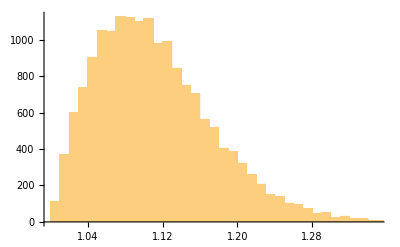

```mathematica
Histogram[trial]
```

```mathematica
Max[trial]
```

1.5158

```mathematica
Min[trial]
```

1.00189

```mathematica
Mean[trial]
```

1.11171